# Shor Code: General Errors

Episode 44. Shor Code: Bit-Flip Errors

Episode 45. Shor Code: Phase-Flip Errors

Episode 46. Shor Code: General Errors

## Errors in Quantum vs Classical States

Errors are continuous: 0 c_0+1 c_1↦0 d_0+1 d_1

Errors include decoherence: 0 c_0+1 c_1↦ρ

No-cloning theorem: Cannot protect a quantum state by simply copies the original

Complementarity principle: A naive detection-and-correction strategy does not work.

### A Big Question

Would it be possible at all to correct “quantum errors”?

## Bit-Flip Code

Codewords: {OverBar[0]:=000, OverBar[1]:=111 }

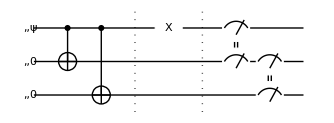

Figure 1. A typical quantum circuit for Shor’s bit-flip code.

### Toolbox

Define a tool function to generate the quantum circuit for bit-flip encoding.

```mathematica
bitFlip[ss:{__?QubitQ}]:=Apply[
QuantumCircuit,
ReleaseHold@Thread[Hold[CNOT][First@ss,Rest[ss]]]
]
```

```mathematica
Let[Qubit,S]
```

```mathematica
ss=S[{1,2,3},$]
```

```mathematica
Hold[CNOT][First@ss,Rest[ss]]
```

```mathematica
Thread[Hold[CNOT][First@ss,Rest[ss]]]
```

```mathematica
ReleaseHold@Thread[Hold[CNOT][First@ss,Rest[ss]]]
```

```mathematica
Let[Qubit,S]
```

```mathematica
bitFlip[S@{1,2,3}]
```

## Phase-Flip Errors

Codewords: {OverBar[0]:=+++, OverBar[1]:=---}

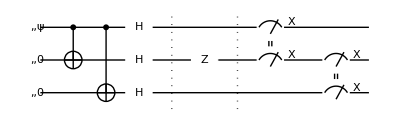

Figure 2. A typical quantum circuit for Shor’s phase-flip code.

### Toolbox

Define a tool function to generate the quantum circuit for bit-flip encoding.

```mathematica
phaseFlip[ss:{__?QubitQ}]:=QuantumCircuit[
bitFlip[ss],
Through[ss[6]]
]
```

```mathematica
Let[Qubit,S]
```

```mathematica
phaseFlip[S@{1,2,3}]
```

## Bit-Flip and/or Phase-Flip Errors

Codewords: {OverBar[0]:=000, OverBar[1]:=111}      (bit-flip code)

Codewords: {OverBar[0]:=+++, OverBar[1]:=---}       (phase-flip code)

Codewords

OverBar[0]:=((000+111)⊗(000+111)⊗(000+111))/(√8) ,

OverBar[1]:=((000-111)⊗(000-111)⊗(000-111))/(√8) .

```mathematica
Let[Qubit,S]
```

We encode a physical single-qubit state into 9 qubits.

```mathematica
$n=9;
kk=Range[$n];
SS=S[kk,$]
```

Here is a quantum circuit for Shor’s 9-qubit quantum error-correction code.

```mathematica
qc=QuantumCircuit[
Ket[S@Range[2,9]],
phaseFlip[S@{1,4,7}],"Separator",
{bitFlip[S@{1,2,3}],bitFlip[S@{4,5,6}],bitFlip[S@{7,8,9}]},
"Invisible"->S@{3.5,6.5}
]
```

This is the logical basis state 0of the 9-qubit code.

```mathematica
ket0=qc**Ket[S[1]->0];
KetFactor@ket0
```

This is the logical basis state 1of the 9-qubit code.

```mathematica
ket1=qc**Ket[S[1]->1];
KetFactor@ket1
```

This is the set of errors against which we can protect our state with the nine-qubit code. Note that included are the Pauli Y operators, which refer to the case of simultaneous bit-flip and phase-flip errors on the same qubit.

```mathematica
errors=Join[S[kk,1],S[kk,3],S[kk,2]]
```

Randomly choose an error from the above set.

```mathematica
err=RandomChoice[errors];
PauliForm[err,S@Range@9];
qc2=QuantumCircuit[qc,"Separator",err]
```

Construct the measurements for error-syndrome detection.

```mathematica
msr=QuantumCircuit[
QuantumCircuit@@@{
Measurement/@{S[1,3]**S[2,3],S[2,3]**S[3,3]},
Measurement/@{S[4,3]**S[5,3],S[5,3]**S[6,3]},
Measurement/@{S[7,3]**S[8,3],S[8,3]**S[9,3]}
},{"Spacer"},
Measurement[Multiply@@S[Range[1,6],1]],{"Spacer"},
Measurement[Multiply@@S[Range[4,9],1]]
]
```

```mathematica
qc3=QuantumCircuit[qc2,"Separator",msr]
```

Now, suppose that we want to encode a single-qubit state to protect it against the bit-flip and phase-flip errors.

```mathematica
Let[Complex,c]
```

```mathematica
in=ProductState[S[1]->{c[0],c[1]},"Label"->Ket[ψ]]
```

Calculate the output state.

```mathematica
out=qc3**in;
```

Extract the observables in the measurements.

```mathematica
gnr=Measurements[msr]
```

Check the measurement outcomes, which tells you where the error occurs and what is the error.

```mathematica
sdr=Readout[gnr]
```

Recover the original logical state .

```mathematica
new=err**out;
```

In the logical basis, the recovered state indeed coincide with the original state.

```mathematica
Dagger[{ket0,ket1}]**new//Simplify
```

## Summary

### Keywords

Bit-flip errors

Phase-flip errors

### Functions

CNOT

Measurement

### Related Links

Section 6.1 of the Quantum Workbook (2022, 2023)

Tutorial: The Nine-Qubit Code